## Testing the grid refinement

```mathematica
Integrate[Sqrt[a/Pi]Exp[-a*x^2],{x,-Infinity,Infinity},Assumptions->a>0]
f=Exp[-a*x^2];
df=Simplify[Abs[D[f,{x,2}]]]
Integrate[df/Sqrt[a],{x,-Infinity,Infinity},Assumptions->a>0]
```

1

2 ⅇ^(-Re[a x^2]) Abs[a-2 a^2 x^2]

4 √(2/ⅇ)

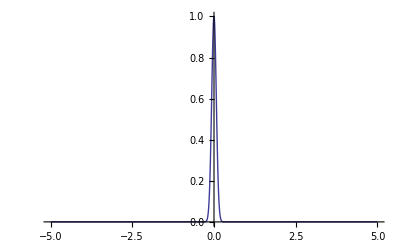

```mathematica
Plot[f/.a->100,{x,-5,5},PlotRange->All]
```

```mathematica
df=Sqrt[E/(32*a)]Abs[D[Exp[-a*(x-0.5)^2],{x,2}]];
```

```mathematica
df/.x->0//Simplify
```

0.291455 √(1/a) ⅇ^(-0.25 Re[a]) Abs[a (-2.+1. a)]

0.291455 √(1/a) ⅇ^(-0.25 Re[a]) Abs[a (-2.+1. a)]

```mathematica
ff=Exp[-a*x^2]
df=Sqrt[E/(32a)]*Abs[D[ff,{x,2}]]//Simplify
```

ⅇ^(-a x^2)

(√(1/a) ⅇ^(1/2-Re[a x^2]) Abs[a-2 a^2 x^2])/(2 √2)

Blue curve is grid representation of the Gaussian after refine_around _points;
Purple curve is the representation after refine_to _function (curvature, cmin, cmax), with the points showing the grid points.
Red dotted curve shows the absolute value of the normalized curvature of the Gaussian -- the density of grid points is proportional to this quantity.

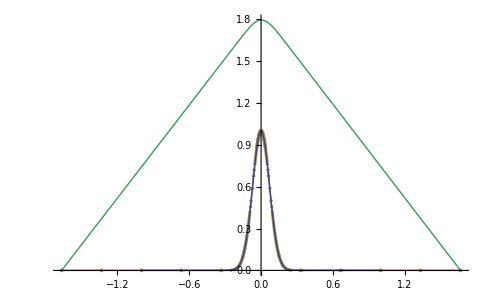

```mathematica
Get["test.m"];
Show[
ListPlot[{coarsedensity,density,density,potential},Joined->{False,True,False,True},AxesOrigin->{0,0},PlotRange->All,PlotStyle->PointSize[.005]],
Plot[f/.a->100.,{x,-1,1},PlotStyle->Thick,PlotRange->All]
]
```

```mathematica
density
```

{{-5.,0.},{-4.,0.},{-3.,0.},{-2.,0.},{-1.,0.000045},{0.,1.},{1.,0.000045},{2.,0.},{3.,0.},{4.,0.},{5.,0.}}

```mathematica
B=A;
B[[1,1]]=2;
last=Length[A];
B[[last,last]]=1;
```

```mathematica
Inverse[B]//MatrixForm
```

(1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 2. | 2. | 2. | 2. | 2. | 2. | 2. | 2. | 2. | 2.
1. | 2. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3.
1. | 2. | 3. | 4. | 4. | 4. | 4. | 4. | 4. | 4. | 4.
1. | 2. | 3. | 4. | 5. | 5. | 5. | 5. | 5. | 5. | 5.
1. | 2. | 3. | 4. | 5. | 6. | 6. | 6. | 6. | 6. | 6.
1. | 2. | 3. | 4. | 5. | 6. | 7. | 7. | 7. | 7. | 7.
1. | 2. | 3. | 4. | 5. | 6. | 7. | 8. | 8. | 8. | 8.
1. | 2. | 3. | 4. | 5. | 6. | 7. | 8. | 9. | 9. | 9.
1. | 2. | 3. | 4. | 5. | 6. | 7. | 8. | 9. | 10. | 10.
1. | 2. | 3. | 4. | 5. | 6. | 7. | 8. | 9. | 10. | 11.)

```mathematica
Get["test.m"];
MatrixForm[A]
```

(1. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-1. | 2. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -1. | 2. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -1. | 2. | -1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -1. | 2. | -1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -1. | 2. | -1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -1. | 2. | -1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -1. | 2. | -1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 2. | -1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 2. | -1.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 1.)

(1. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-1. | 2. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -1. | 2. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -1. | 2. | -1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -1. | 2. | -1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -1. | 2. | -1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -1. | 2. | -1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -1. | 2. | -1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 2. | -1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 2. | -1.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 1.)

(1. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-1. | 2. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -1. | 2. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -1. | 2. | -1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -1. | 2. | -1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -1. | 2. | -1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -1. | 2. | -1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -1. | 2. | -1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 2. | -1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 2. | -1.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 1.)

(1.6 | -1.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-1.6 | 3.2 | -1.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -1.6 | 3.2 | -1.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -1.6 | 3.2 | -1.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -1.6 | 3.2 | -1.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -1.6 | 3.2 | -1.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -1.6 | 3.2 | -1.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -1.6 | 3.2 | -1.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.6 | 3.2 | -1.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.6 | 3.2 | -1.6 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.6 | 3.2 | -1.6 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.6 | 3.2 | -1.6 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.6 | 3.2 | -1.6 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.6 | 3.2 | -1.6 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.6 | 3.2 | -1.6 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.6 | 3.2 | -1.6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.6 | 1.6)

(0.8 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8
0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 0.8)

(0.8 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 0.8)

(0.8 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 0.8)

(0.8 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 1.6 | -0.8
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.8 | 0.8)

```mathematica
b
```

{0.,0.03542,0.177434,0.355811,0.663121,0.880748,1.14857,1.47066,1.84891,2.28226,2.76606,3.84593,4.96972,5.49628,5.96834,6.36335,6.5256,6.66141,6.769,6.84691,6.89409,6.90988,6.89409,6.84691,6.769,6.66141,6.5256,6.36335,5.96834,5.49628,4.96972,3.84593,2.76606,2.28226,1.84891,1.47066,1.14857,0.880748,0.663121,0.355811,0.177434,0.03542,0.000586,0.}

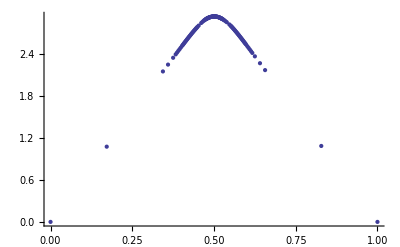

```mathematica
ListPlot[potential]
```

```mathematica
V=Interpolation[potential];
```

```mathematica
DV=D[V[x],x]
DDV=D[V[x],{x,2}];
DDVb=D[D[V[x],x],x];
```

InterpolatingFunction[{{0.,1.}},<>][x]

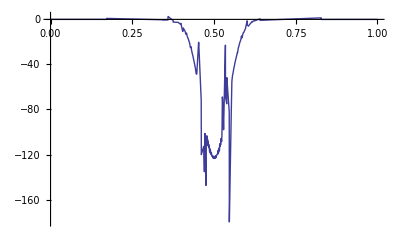

```mathematica
Plot[{DDVb},{x,0,1},PlotRange->All]
```

```mathematica
d[f_]:=Table[{f[[i,1]],(f[[i+1,2]]-f[[i,2]])/((f[[i+1,1]]-f[[i,1]]))},{i,Length[f]-1}];
```

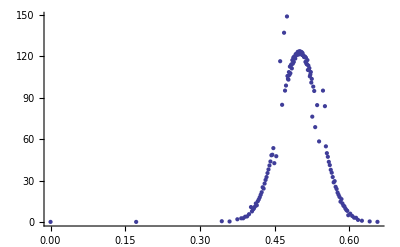

```mathematica
ListPlot[{#[[1]],-#[[2]]}&/@d[d[potential]]]
```

```mathematica
DV/.x->0
```

6.26233

```mathematica
Dimensions[A]
```

{9,9}

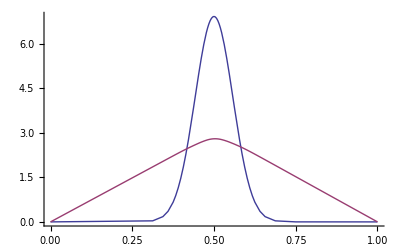

```mathematica
Get["test.m"];
ListPlot[{density,potential},Joined->True]
last=Length[A];
A[[1,1]]=1;
A[[last,last]]=1;
A[[2,1]]=0;
A[[1,2]]=0;
A[[last-1,last]]=0;
A[[last,last-1]]=0;
A//MatrixForm;
```

```mathematica
X
```

{23.2567,25.5824,26.7447,27.9042,28.4812,29.053,29.6179,30.1738,30.7183,31.2483,32.2726,33.2538,33.7143,34.136,34.5148,34.6808,34.822,34.9377,35.0274,35.0907,35.1272,35.1368,35.1194,35.075,35.0039,34.9064,34.7828,34.4848,34.137,33.7425,32.8678,31.9154,31.4092,30.8813,30.3356,29.7755,29.2039,28.6233,27.4484,26.2631,23.8814,19.1069,0.000586,0.}

```mathematica
Xp=LinearSolve[4Pi*A,b];
Xp[[1]]=0;
Xp[[last]]=0;
```

```mathematica
#[[2]]&/@potential
Xp
```

{0.,1.85071,2.03578,2.12828,2.22055,2.26646,2.31196,2.35692,2.40116,2.44448,2.48666,2.56818,2.64625,2.6829,2.71646,2.7466,2.75981,2.77105,2.78026,2.7874,2.79243,2.79533,2.7961,2.79471,2.79118,2.78552,2.77776,2.76793,2.74421,2.71653,2.68515,2.61554,2.53975,2.49946,2.45746,2.41403,2.36946,2.32397,2.27777,2.18427,2.08995,1.90042,1.52048,0.}

{0,1.87566,2.06314,2.15665,2.24973,2.29586,2.34143,2.3863,2.43025,2.47305,2.51443,2.59375,2.66829,2.70248,2.73324,2.76029,2.77184,2.78136,2.78881,2.79416,2.79737,2.79845,2.79737,2.79416,2.78881,2.78136,2.77184,2.76029,2.73324,2.70248,2.6683,2.59375,2.51443,2.47305,2.43025,2.3863,2.34144,2.29586,2.24973,2.15666,2.06314,1.87566,1.50053,0}

## How does the Laplacian look when using piecewise linear basis functions?

```mathematica
cells={{0,.2},{.2,1}};
shapeleft[{a_,b_}]:=Piecewise[{{(x-a)/(b-a),x≥a&&x≤b},{0,True}}]
shaperight[{a_,b_}]:=Piecewise[{{1-(x-a)/(b-a),x≥a&&x≤b},{0,True}}]
```